## Calculus III Lab #6 : Work in a Vector Field

### In this lab, we will find the work done in a vector field around a square. The square will go from ( -1, -1 ) to ( 1, -1 ) to ( 1, 1 ) to ( -1, 1 ) to ( -1, -1 ). Let us us suppose the vector field is F( x, y ) = < y, 2x >.

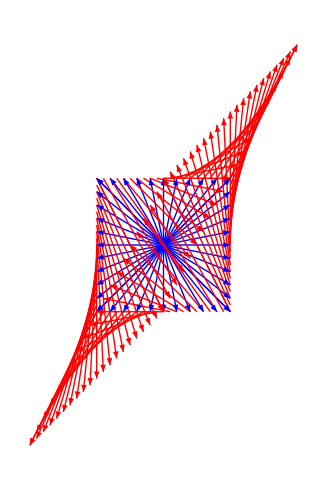

```mathematica
Clear[f,g,x,y]
f[x_,y_]:=y;
g[x_,y_]:= 2x;
force1=Graphics[{RGBColor[1,0,0],Table[Arrow[{{i,j},{i+f[i,j],j+g[i,j]}}],{i,-1,1,0.1},{j,-1,-1,0.1}]}];
force2=Graphics[{RGBColor[1,0,0],Table[Arrow[{{i,j},{i+f[i,j],j+g[i,j]}}],{i,1,1,0.1},{j,-1,1,0.1}]}];
force3=Graphics[{RGBColor[1,0,0],Table[Arrow[{{i,j},{i+f[i,j],j+g[i,j]}}],{i,1,-1,-0.1},{j,1,1,0.1}]}];
force4=Graphics[{RGBColor[1,0,0],Table[Arrow[{{i,j},{i+f[i,j],j+g[i,j]}}],{i,-1,-1,0.1},{j,1,-1,-0.1}]}];
path1 = Graphics[{RGBColor[0,0,1],Table[Arrow[{{0,0},{2t-1,-1}}],{t,0,1,0.1}]}];
path2 = Graphics[{RGBColor[0,0,1],Table[Arrow[{{0,0},{1,2t-3}}],{t,1,2,0.1}]}];
path3 = Graphics[{RGBColor[0,0,1],Table[Arrow[{{0,0},{-2t+5,1}}],{t,2,3,0.1}]}];
path4 = Graphics[{RGBColor[0,0,1],Table[Arrow[{{0,0},{-1,-2t+7}}],{t,3,4,0.1}]}];
Show[path1,path2,path3,path4,force1,force2,force3,force4,AspectRatio->Automatic]
```

```mathematica
w1=∫_0^1 {-1,4t-2}.{2,0}ⅆt;
w2= ∫_1^2 {2t-3,2}.{0,2}ⅆt;
w3=∫_2^3 {1,-4t+10}.{-2,0}ⅆt;
w4= ∫_3^4 {-2t+7,-2}.{0,-2}ⅆt;
wTotal = w1+w2+w3+w4
g=∫_-1^1 ∫_-1^1 ( D[g[x,y],x]-D[f[x,y],y])ⅆyⅆx
```

4

4

### Exercise 1. Use the above vector field with a circular path of radius 1. Find the work done in 2 ways. 2. Design your own vector field and path. Find work done in 2 ways.

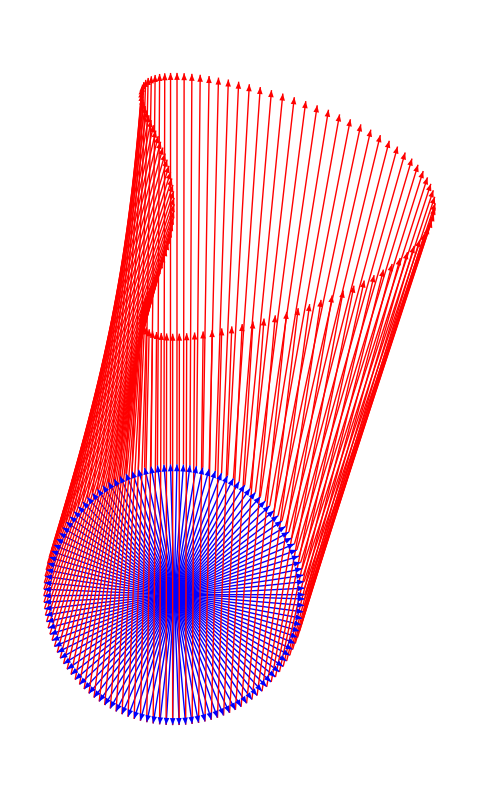

```mathematica
Clear[f,g,x,y]
f[x_,y_]:=x^2;
g[x_,y_]:=3
force1=Graphics[{RGBColor[1,0,0],Table[Arrow[{{Cos[i],Sin[i]},{Cos[i]+f[Cos[i],Sin[i]],Sin[i]+g[Cos[i],Sin[i]]}}],{i,0,2π,0.05}]}];
path1 = Graphics[{RGBColor[0,0,1],Table[Arrow[{{0,0},{Cos[t],Sin[t]}}],{t,0,2π,0.05}]}];
Show[path1,force1,AspectRatio->Automatic]
```